```mathematica
SetDirectory["/Users/chris/Dropbox/Lawnmower"];
fNames=FileNames["*.csv"];
```

```mathematica
fNames[[1]]
```

F127NHSpeptide_MotileTrajs_all_20220126.csv

```mathematica
fNames[[2]]
```

F127NHSpeptide_NONMotileTrajs_all_20220126.csv

```mathematica
traj1=Import[fNames[[1]]][[3;;-1]]ᵀ;
traj2=Import[fNames[[2]]][[3;;-1]]ᵀ;
```

```mathematica
paths1=Flatten[#,{{2},{1}}]&/@Flatten[{traj1[[2;;-1;;2]],traj1[[3;;-1;;2]]},{{2},{1}}];
paths2=Flatten[#,{{2},{1}}]&/@Flatten[{traj2[[2;;-1;;2]],traj2[[3;;-1;;2]]},{{2},{1}}];
```

```mathematica
(* Drops the first "dropNumber" elements and then places the first point at the origin *)
dropNumber=0;
rpaths1=TakeWhile[#-ConstantArray[#[[1]],Length[#]],NumericQ[#[[1]]]&&NumericQ[#[[2]]]&]&/@(Drop[#,dropNumber]&/@paths1);
rpaths2=TakeWhile[#-ConstantArray[#[[1]],Length[#]],NumericQ[#[[1]]]&&NumericQ[#[[2]]]&]&/@(Drop[#,dropNumber]&/@paths2);
```

```mathematica
(* Combined data set of Motile and NONMotile trajectories *)
allPaths=Join[rpaths1,rpaths2];
```

```mathematica
(* First differenced paths (i.e x(1+1)-x(i)) *) 
difPaths=Differences[#]&/@allPaths;
```

```mathematica
(* First differenced paths in Polar Coordinates. There are some points were the particle did not move at all in the 100'th path, i.e. the first difference on the position is (0,0). This leads to the error messages, but this can be igored.  *)
polDifPaths=ToPolarCoordinates/@difPaths;
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

```mathematica
(* The first difference in the angle coordinate of the first differences *)
difDifAngles=Mod[Differences[#[[;;,2]]],2π,-π]&/@polDifPaths;
```

```mathematica
(* This list is the jump length and the angle diff. This allows us to look at how the direction of the path changes after a jump. *)
jumpAngles=Table[{polDifPaths[[i]][[1;;-2,1]],difDifAngles[[i]]}ᵀ,{i,1,Length[polDifPaths]}];
```

```mathematica
fulJumpAngleSet=Flatten[jumpAngles,1];
```

```mathematica
Histogram3D[Select[fulJumpAngleSet,#[[1]]>2&]]
```

-Graphics3D-

```mathematica
Export["jLengthAngle.csv",fulJumpAngleSet];
```

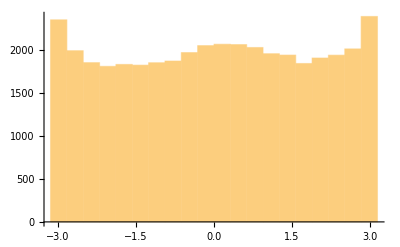
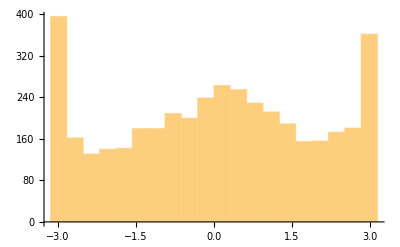
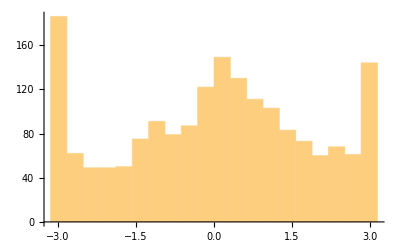
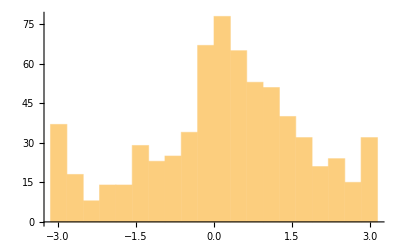
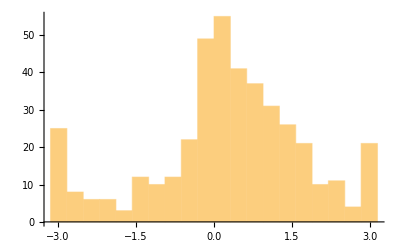
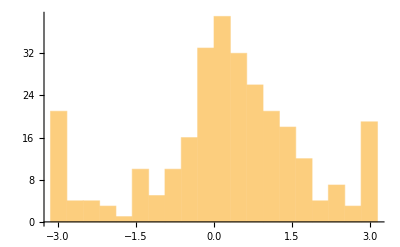
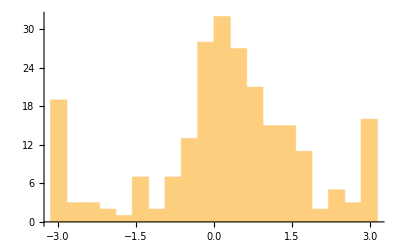
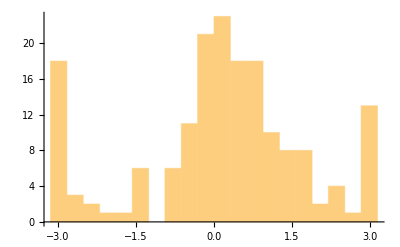

```mathematica
ptabs=Table[Histogram[Select[fulJumpAngleSet,#[[1]]>j&][[;;,2]],{-π,π,π/10}],{j,1,10}]
```

```mathematica
Do[Export["HistogramWithCutoffOf"<>ToString[j]<>".pdf",ptabs[[j]]],{j,1,Length[ptabs]}]
```

```mathematica
Histogram3D[Flatten[jumpAngles,1]]
```

-Graphics3D-

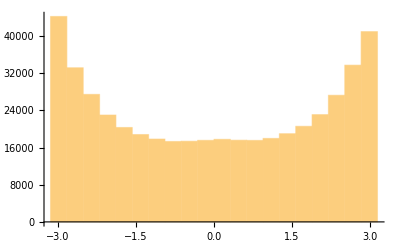

```mathematica
Histogram[Flatten[difDifAngles],{-π,π,π/10}]
```